# Contouring: Marching Cubes and Dual Contouring

CSE 554 Module 3, Washington University in St. Louis (Fall 2018)

## Introduction

Iso-contours are loci of points having a specific value, called iso-value, in a density function. They are commonly used for data visualization and processing. You will implement some popular contouring algorithms in 2D and 3D.

There are many chances of earning extra credit points in this module. You are required to implement either the primal method (Marching Squares, Marching Cubes) or the dual method (Dual Contouring). Implementing both methods will be extra credit. Also, you can earn more extra credit by implementing some ways of speeding up the contouring algorithm (as we discussed in lecture Contouring II).

## Helpers

In this and subsequent modules, you will be dealing with polylines (in 2D) and meshes (in 3D). A common way of representing them is separately list the geometry (e.g., the X,Y,Z coordinates of vertices) and the connectivity (e.g., what vertices make up a triangle).

For example,  a 2D polyline is a list of two lists {V,E}, where V is a list of vertex coordinates (with X,Y components), and E is a list of edges, each consisting of the indices of its two vertices. Here is a polyline with 3 vertices and 2 edges:

```mathematica
mypoly={{{1.5,1.5},{1.7,2},{2,3}},{{1,2},{2,3}}};
```

Note that the indices of vertices in the edge list {{1,2},{2,3}} starts from 1.

Similarly, a 3D mesh is a list of two lists {V,T}, where V is a list of vertex coordinates (with X,Y,Z components), and T is a list of polygons, each consisting of the indices of its vertices. Here is a mesh with 4 vertices and 2 triangles:

```mathematica
mymesh={{{0,0,0},{1,0,0},{0,1,0},{0,0,1}},{{1,2,3},{1,2,4}}};
```

### Importing images

Sets the default folder to be the folder where this notebook is saved.

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

Constructs a 2D array from input RGB color images by extracting the Red component of each pixel.

```mathematica
PNGtoGray[filename_]:=Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
```

```mathematica
GIFtoGray[filename_]:=255-Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
```

### Showing images

Shows a grayscale image. Note that I added a Transpose and shifted the image by {.5,.5} so that the image will be displayed in the same coordinate system of your iso-curves.

```mathematica
showGrayImage[img_]:=Graphics[Raster[Transpose[(img-Min[img])/(Max[img]-Min[img])],{{.5,.5},Dimensions[img]+.5}],Frame->False];
```

### Showing polylines

This function displays a 2D polyline {V,E} where V is the vertex list and E is the edge list. The function takes in an additional parameter of color (e.g., GrayLevel or RGB).

```mathematica
showCurve[{V_,E_},col_]:=Graphics[{{col,Map[Line[V⟦#⟧]&,E]},Map[Point,V]},Frame->False];
```

For example, let's draw mypoly defined above:

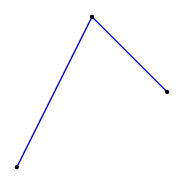

```mathematica
showCurve[mypoly,RGBColor[0,0,1]]
```

Same as above, except the vertices will not be displayed. This is helpful if you have lots of vertices in the curve.

```mathematica
showCurveNoPoints[{V_,E_},col_]:=Graphics[{col,Map[Line[V⟦#⟧]&,E]},Frame->False];
```

### Showing meshes

This function displays a 3D mesh {V,T} where V is the vertex list and T is the triangle list. The function takes in an additional parameter of color (e.g., GrayLevel or RGB).

```mathematica
showSurface[{V_,T_},col_]:=Graphics3D[{col,Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral"];
```

For example, let's draw mymesh defined above:

```mathematica
showSurface[mymesh,RGBColor[1,0,0]]
```

-Graphics3D-

Same as agove, except the polygon edges will not be displayed. This is helpful if you have lots of polygons in the surface.

```mathematica
showSurfaceNoEdges[{V_,T_},col_]:=Graphics3D[{col,EdgeForm[{}],Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral"];
```

## Algorithms

### Computing iso-curves in 2D [6 + 8 pts]

Algorithm 1: [4pts, Extra credit 4 pts] Create a function that takes in a grayscale image and an iso-value, and outputs an iso-curve. Use either Marching Square or Dual Contouring. Implementing a second algorithm gives you extra credit! The iso-curve should be represented as a polyline {V,E}, where V is a list of vertex coordinates (with X,Y components), and E is a list of edges, each consisting of the indices of its two vertices. 

Notes:
1. Assume that the X,Y coordinates of the lower-left corner pixel of the image are {1,1}, and each pixel has size 1.

2. Make sure you don't create the same vertex twice. You can either create an additional array twice as large as the input to store the indices of the vertices after they are created. Alternatively, for better space efficiency (but not as fast), use a hash map to store the index of the created vertex on a grid edge.

3. Take care of the degenerate case where a pixel's value is identical with the iso-value. You can either treat it as above or below the iso-value in your code, just be consistent with your choice for all such pixels.

```mathematica
(*for configuration table*)
twoBytwoMap[pixel1_,pixel2_,pixel3_,pixel4_]:=Module[{val},
val=If[pixel1≥0,1,0]*1000+If[pixel2≥0,1,0]*100+If[pixel3≥0,1,0]*10+If[pixel4≥0,1,0];
val
]
```

```mathematica
configTable2D[fourValues_]:=Module[{config},
config=Which[
fourValues==0,{},
fourValues==1,{{2,4}},
fourValues==10,{{2,3}},
fourValues==11,{{3,4}},
fourValues==100,{{1,4}},
fourValues==101,{{1,2}},
fourValues==110,{{2,3},{1,4}},
fourValues==111,{{1,3}},
fourValues==1000,{{1,3}},
fourValues==1001,{{1,3},{2,4}},
fourValues==1010,{{1,2}},
fourValues==1011,{{1,4}},
fourValues==1100,{{3,4}},
fourValues==1101,{{2,3}},
fourValues==1110,{{2,4}},
fourValues==1111,{}
];
config
]
```

```mathematica
configTable2D[1111]
```

{}

```mathematica
getEdgeCoorByNumber[num_,x_,y_]:=Module[{edgeCoor},
edgeCoor=Which[
(*top edge*)
num==1,{2*x,2*y+1},
(*bottom edge*)
num==2,{2*x,2*y-1},
(*left edge*)
num==3,{2*x-1,2*y},
(*right edge*)
num==4,{2*x+1,2*y}];
edgeCoor
]
```

```mathematica
interpolate[edge1234_,x_,y_,img_]:=Module[{vertexPosition,blackPixelIndex,whitePixelIndex,f0,f1,t,xf,yf,result},
(*edge1234 is either 1,2,3,or 4;
1 is the top edge, 2 is the bot edge, 3 is the left, 4 is the right;
f1 is the nonnegative value;f0 is negative*)
vertexPosition=Which[
edge1234==1,{{x,y+1},{x+1,y+1}},
edge1234==2,{{x,y},{x+1,y}},
edge1234==3,{{x,y},{x,y+1}},
edge1234==4,{{x+1,y},{x+1,y+1}}];

blackPixelIndex=If[img⟦vertexPosition⟦1,1⟧,vertexPosition⟦1,2⟧⟧<0,{vertexPosition⟦1,1⟧,vertexPosition⟦1,2⟧},{vertexPosition⟦2,1⟧,vertexPosition⟦2,2⟧}];
whitePixelIndex=If[img⟦vertexPosition⟦1,1⟧,vertexPosition⟦1,2⟧⟧≥0,{vertexPosition⟦1,1⟧,vertexPosition⟦1,2⟧},{vertexPosition⟦2,1⟧,vertexPosition⟦2,2⟧}];

f0=If[img⟦vertexPosition⟦1,1⟧,vertexPosition⟦1,2⟧⟧<0,img⟦vertexPosition⟦1,1⟧,vertexPosition⟦1,2⟧⟧,img⟦vertexPosition⟦2,1⟧,vertexPosition⟦2,2⟧⟧];
f1=If[img⟦vertexPosition⟦1,1⟧,vertexPosition⟦1,2⟧⟧≥0,img⟦vertexPosition⟦1,1⟧,vertexPosition⟦1,2⟧⟧,img⟦vertexPosition⟦2,1⟧,vertexPosition⟦2,2⟧⟧];

t=f0/(f0-f1);
xf=blackPixelIndex⟦1⟧+t*(whitePixelIndex⟦1⟧-blackPixelIndex⟦1⟧);
yf=blackPixelIndex⟦2⟧+t*(whitePixelIndex⟦2⟧-blackPixelIndex⟦2⟧);
result={xf,yf};
result
];
```

```mathematica
bigEdgeUsageTable[dimN_,dimM_]:=Module[{bigTable},
(*create a 2m*1 x 2n*1 table to document edge usage*)
bigTable=Table[0,{i,2*dimN+1},{j,2*dimM+1}];bigTable];
extractZeroContour2D[img_,iso_]:=Map[#-iso&,img,{2}];
```

```mathematica
contour2D[img_,iso_]:=Module[{imgZeroOut,dataTable,dimN,dimM,config,imgEdgeCoor1,imgEdgeCoor2,v1,v2,myPolyV,myPolyVIndex,myEdge,myPolyE,myPolyEIndex,myPoly},
(*initialize empty vertices and edges' set;initialize v1,v2*)
myPolyV={};myPolyE={};v1=0;v2=0;
myPolyVIndex=1;
myPolyEIndex=1;
(*get the dimension of the image*)
 {dimN,dimM}=Dimensions[img];
(*Here for each pixel we substruct the iso value*)
imgZeroOut=extractZeroContour2D[img,iso];
(*We also want to keep track of whether the vertex between pixel has been computed;
0 is the default -- not used, otherwise we store an index (index > 0)*)
dataTable=bigEdgeUsageTable[dimN,dimM];
Do[
(*get the configuration for this 2 by 2 pixel grid*)
config=configTable2D[twoBytwoMap[imgZeroOut⟦i,j+1⟧,imgZeroOut⟦i+1,j+1⟧,imgZeroOut⟦i,j⟧,imgZeroOut⟦i+1,j⟧]];

Do[
(*loop thru the edges that we are going to to build up one at a time*)
imgEdgeCoor1=getEdgeCoorByNumber[config⟦k,1⟧,i,j];
imgEdgeCoor2=getEdgeCoorByNumber[config⟦k,2⟧,i,j];
(*
Print["At ",i ,", ",j];*)

v1=If[dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧⟧≠0,
(*return the index right away*)
dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧⟧,
(*otherwise, append the vertex, record the index, increment the index value, return the index*)
myPolyV=Append[myPolyV,interpolate[config⟦k,1⟧,i,j,imgZeroOut]];
dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧⟧=myPolyVIndex;
myPolyVIndex++;
dataTable⟦imgEdgeCoor1⟦1⟧,imgEdgeCoor1⟦2⟧⟧];

v2=If[dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧⟧≠0,dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧⟧,
myPolyV=Append[myPolyV,interpolate[config⟦k,2⟧,i,j,imgZeroOut]];
dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧⟧=myPolyVIndex;
myPolyVIndex++;
dataTable⟦imgEdgeCoor2⟦1⟧,imgEdgeCoor2⟦2⟧⟧];

(*push the edge into the edge set*)
myEdge={v1,v2};
myPolyE=Append[myPolyE,myEdge];
myPolyEIndex++;
,{k,Length[config]}];

,{i,dimN-1},{j,dimM-1}];
myPoly={myPolyV,myPolyE};
myPoly
]
```

Testing: [2pts] Test your algorithm on the following two examples, a synthetic image created by a function, and a grayscale image loaded from a file. For each example:

1. Use showCurve (in the Helpers) to verify the result of your function with the input image. You can simultaneously show the curve and the original image by the Show command.

2. Make a Manipulate applet that displays the results at varying iso-values (check with Module 0 if you forgot how to use Manipulate).

3. The following showMathematica function displays the result of Mathematica's built-in contouring function (ListContourPlot). Show your result overlaying on Mathematica's (by combining them with Show command).

```mathematica
p=contour2D[imgSyn,.3];
```

```mathematica
showMathematica[img_,iso_]:=ListContourPlot[Transpose[img],Contours->{iso},ContourShading->None,ContourStyle->RGBColor[0,0,1],Frame->False,DataRange->Transpose[{{1,1},Dimensions[img]}]];
```

Example 1: A synthetic image (feel free to change the resolution of the image to test your code)

```mathematica
imgSyn=Table[N[Sin[x]Sin[y]],{x,0,2π,2π/20},{y,0,2π,2π/20}];
```

The Mathematica's contour looks like:

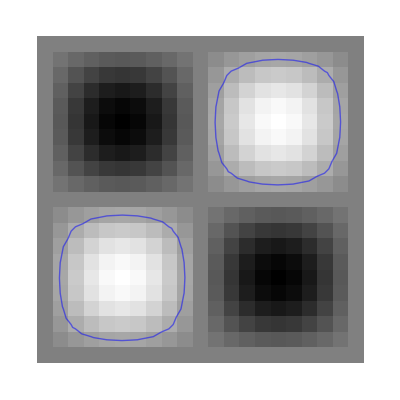

```mathematica
Show[showGrayImage[imgSyn],showMathematica[imgSyn,.3]]
```

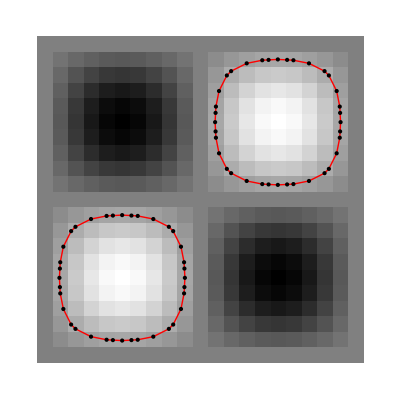

```mathematica
Show[showGrayImage[imgSyn],showCurve[p,RGBColor[1,0,0]]]
```

Example 2: The image in the file "cryo.gif", which is a 2D slice of  3D density volume of a protein imaged by cryo-electron microscopy.

```mathematica
imgCryo=GIFtoGray["cryo.gif"];
```

The Mathematica's contour looks like:

```mathematica
Show[showGrayImage[imgCryo],showMathematica[imgCryo,120]]
```

-Graphics-

```mathematica
Show[showGrayImage[imgCryo],showCurve[contour2D[imgCryo,120],RGBColor[1,0,0]]]
```

-Graphics-

Algorithm 2: [Extra credit 4 pts] Design a more efficient algorithm for contouring using either a Quadtree or Interval Tree. Test it out with the examples above (show that the results are identical to those of un-accelerated contouring, and demonstrates the speed-up using Mathematica's Timing function).

### Computing iso-surfaces in 3D [6 + 8 pts]

About Marching Cubes look-up table: The algorithm uses a look-up table to determine how the vertices in a grid cube are connected into triangles. In the data folder, you will find a table I made in Mathematica format ("cycles.txt"). The table contains 256 entries, one for each sign combination of the eight cube corners. Each entry is a list of "cycles" consisting of grid edges of the cube whose vertices should be connected to form a polygon (which may further need to be triangulated).

To use the table, load it first as a Mathematica list:

```mathematica
cycles=Get["cycles.txt"];
```

Let's look at one entry of the table:

```mathematica
cycles⟦131⟧
```

{{{1,2},{1,5},{1,3}},{{3,7},{5,7},{7,8}}}

This entry consists of two lists, called cycles. A cycle is a list of grid edges, where each grid edge is represented by indices of its two grid points. Each cycle represents a polygon to be created, whose vertices lie on the grid edges in the cycle. In the case above, both cycles have 3 grid edges, hence they represent two triangles to be built. In general, a cycle may contain more than 3 grid edges, in which case you will need to tessellate the polygon into triangles (e.g., like a fan). The indexing of the eight corners of the cube is shown below:

-Graphics-

The index of the entries in the table can be computed from the sign combination at the cube corners in the following way: say all corners are all negative except corners 1 and 7 which are positive. This combination corresponds to the entry with index 10000010 (in base-2) + 1=131 (in decimal), where the binary form has 1 at its 1st and 7th positions. Check out Mathematica's FromDigits function to find out how to create a base-2 number.

To get a better idea of how to use the look-up table, check out the following code that interactively displays the cycles in the table for any given sign combination:

```mathematica
(* locations of 8 cube corners *)
verts=Flatten[Table[{i,j,k},{i,0,1},{j,0,1},{k,0,1}],2];
(* applet *)
Manipulate[signs={v1,v2,v3,v4,v5,v6,v7,v8};
Graphics3D[{
(* draw the cube *)
{Opacity[0],Cuboid[]},
(* draw the cube corners *)
MapThread[{GrayLevel[#2],Cuboid[#1-{.05,.05,.05},#1+{.05,.05,.05}]}&,{verts,signs}],
If[showText,{RGBColor[1,0,0],Table[Text[Style["v"<>ToString[i],20],(verts⟦i⟧-{.5,.5,.5})*1.2+{.5,.5,.5}],{i,8}]},{}],
(* draw the vertices on edges *)
If[showVert,{PointSize[.05],RGBColor[1,.2,.2],Map[Map[Point[Mean[verts⟦#⟧]]&,#]&,cycles⟦FromDigits[signs,2]+1⟧]},{}],
(* draw the triangles *)
If[showPoly,{Opacity[.8],RGBColor[.2,.2,1],Map[Polygon[Map[Mean[verts⟦#⟧]&,#]]&,cycles⟦FromDigits[signs,2]+1⟧]},{}]},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"],
{v1,{0,1}},{v2,{0,1}},{v3,{0,1}},{v4,{0,1}},{v5,{0,1}},{v6,{0,1}},{v7,{0,1}},{v8,{0,1}},{showText,{True,False}},{showPoly,{True,False}},{showVert,{True,False}}]
```

```mathematica
makeConfigList[img_,x_,y_,z_]:=Module[{v1,v2,v3,v4,v5,v6,v7,v8,result},
(*Here we make a list so can refer to cycle.txt to see what edges are presented in this voxel's configuration*)
v1=If[img⟦x,y,z⟧≥0,1,0];
v2=If[img⟦x,y,z+1⟧≥0,1,0];
v3=If[img⟦x,y+1,z⟧≥0,1,0];
v4=If[img⟦x,y+1,z+1⟧≥0,1,0];
v5=If[img⟦x+1,y,z⟧≥0,1,0];
v6=If[img⟦x+1,y,z+1⟧≥0,1,0];
v7=If[img⟦x+1,y+1,z⟧≥0,1,0];
v8=If[img⟦x+1,y+1,z+1⟧≥0,1,0];
result={v1,v2,v3,v4,v5,v6,v7,v8};
result
]
```

```mathematica
getEdgeCoorByNumber3D[edge_,x_,y_,z_]:=Module[{edgeCoor},
edgeCoor=Which[
edge=={1,3},{2*x-1,2*y,2*z-1},
edge=={1,2},{2*x-1,2*y-1,2*z},
edge=={2,4},{2*x-1,2*y,2*z+1},
edge=={3,4},{2*x-1,2*y+1,2*z},
edge=={2,6},{2*x,2*y-1,2*z+1},
edge=={1,5},{2*x,2*y-1,2*z-1},
edge=={5,6},{2*x+1,2*y-1,2*z},
edge=={6,8},{2*x+1,2*y,2*z+1},
edge=={7,8},{2*x+1,2*y+1,2*z},
edge=={5,7},{2*x+1,2*y,2*z-1},
edge=={4,8},{2*x,2*y+1,2*z+1},
edge=={3,7},{2*x,2*y+1,2*z-1}
];
edgeCoor
]
```

```mathematica
bigEdgeUsageTable3D[dimX_,dimY_,dimZ_]:=Module[{bigTable},
(*create a 2m*1 x 2n*1 table to document edge usage*)
bigTable=Table[0,{i,2*dimX+1},{j,2*dimY+1},{k,2*dimZ+1}];bigTable];
extractZeroContour3D[img_,iso_]:=Map[#-iso&,img,{3}];
```

```mathematica
getCoor[configQ_,x_,y_,z_]:=Module[{v},
v=Which[
configQ==1,{x,y,z},
configQ==2,{x,y,z+1},
configQ==3,{x,y+1,z},
configQ==4,{x,y+1,z+1},
configQ==5,{x+1,y,z},
configQ==6,{x+1,y,z+1},
configQ==7,{x+1,y+1,z},
configQ==8,{x+1,y+1,z+1}
];
v
]
```

```mathematica
interpolate3D[configQ_,x_,y_,z_,img_]:=Module[{v1,v2,blackPixelIndex,whitePixelIndex,f0,f1,t,xf,yf,zf,result},
(*edge1234 is either 1,2,3,or 4;
1 is the top edge, 2 is the bot edge, 3 is the left, 4 is the right;
f1 is the nonnegative value;f0 is negative*)
v1=getCoor[configQ⟦1⟧,x,y,z]; (*form: {x,y,z} that corresponds to the pixel*)
v2=getCoor[configQ⟦2⟧,x,y,z];

blackPixelIndex=If[img⟦v1⟦1⟧,v1⟦2⟧,v1⟦3⟧⟧<0,v1,v2];
whitePixelIndex=If[img⟦v1⟦1⟧,v1⟦2⟧,v1⟦3⟧⟧≥0,v1,v2];

f0=If[img⟦v1⟦1⟧,v1⟦2⟧,v1⟦3⟧⟧<0,img⟦v1⟦1⟧,v1⟦2⟧,v1⟦3⟧⟧,img⟦v2⟦1⟧,v2⟦2⟧,v2⟦3⟧⟧];
f1=If[img⟦v1⟦1⟧,v1⟦2⟧,v1⟦3⟧⟧≥0,img⟦v1⟦1⟧,v1⟦2⟧,v1⟦3⟧⟧,img⟦v2⟦1⟧,v2⟦2⟧,v2⟦3⟧⟧];

t=f0/(f0-f1);
xf=blackPixelIndex⟦1⟧+t*(whitePixelIndex⟦1⟧-blackPixelIndex⟦1⟧);
yf=blackPixelIndex⟦2⟧+t*(whitePixelIndex⟦2⟧-blackPixelIndex⟦2⟧);
zf=blackPixelIndex⟦3⟧+t*(whitePixelIndex⟦3⟧-blackPixelIndex⟦3⟧);
result={xf,yf,zf};
result
];
```

Algorithm 3: [4 pts, Extra credit 4 pts] Create a function that takes in a grayscale volume and an iso-value, and outputs an iso-surface. Use either Marching Cubes or Dual Contouring. Implementing a second algorithm gives you extra credit! The iso-surface should be represented as a triangular mesh {V,T}, where V is a list of vertex coordinates (with X,Y,Z components), and T is a list of triangles, each consisting of the indices of its three vertices.

Notes: Assume that the X,Y,Z coordinates of the lower-left-near corner voxel of the volume are {1,1,1}, and each voxel has size 1. Other notes from the iso-curve algorithm apply here too.

```mathematica
contour3D[img_,thr_]:=Module[{imgZeroOut,dataTable,dimX,dimY,dimZ,config,imgEdgeCoor,v,myMeshV,myMeshVIndex,myMeshTtemp,myMeshT,myMeshTIndex,myMesh,tessellate1,tessellate2},
(*initialize empty vertices and triangles' set;initialize v1,v2,v3*)
myMeshV={};myMeshT={};v=0;
myMeshVIndex=1;
myMeshTIndex=1;
(*get the dimension of the image*)
 {dimX,dimY,dimZ}=Dimensions[img];
(*Here for each pixel we substruct the iso value*)
imgZeroOut=extractZeroContour3D[img,thr];
(*We also want to keep track of whether the vertex between pixel has been computed;
0 is the default -- not used, otherwise we store an index (index > 0)*)
dataTable=bigEdgeUsageTable3D[dimX,dimY,dimZ];

Do[
config=cycles⟦FromDigits[makeConfigList[imgZeroOut,i,j,k],2]+1⟧;
Do[
(*for each polygon*)
myMeshTtemp={};
Do[
(*Print[config];*)
(*for each edge in the triangle;
this is the dataTable's corresponding index*)

imgEdgeCoor=getEdgeCoorByNumber3D[config⟦q,s⟧,i,j,k];
v=If[dataTable⟦imgEdgeCoor⟦1⟧,imgEdgeCoor⟦2⟧,imgEdgeCoor⟦3⟧⟧≠0,
(*return the index right away*)
dataTable⟦imgEdgeCoor⟦1⟧,imgEdgeCoor⟦2⟧,imgEdgeCoor⟦3⟧⟧,
(*otherwise, append the vertex, record the index, increment the index value, return the index*)
myMeshV=Append[myMeshV,interpolate3D[config⟦q,s⟧,i,j,k,imgZeroOut]];
dataTable⟦imgEdgeCoor⟦1⟧,imgEdgeCoor⟦2⟧,imgEdgeCoor⟦3⟧⟧=myMeshVIndex;
myMeshVIndex++;
dataTable⟦imgEdgeCoor⟦1⟧,imgEdgeCoor⟦2⟧,imgEdgeCoor⟦3⟧⟧];

myMeshTtemp=Append[myMeshTtemp,v];

(*Apply tessellation*)
myMeshTtemp=If[s≥3,
myMeshT=Append[myMeshT,myMeshTtemp];
{myMeshTtemp⟦1⟧,myMeshTtemp⟦3⟧},myMeshTtemp];

,{s,Length[config⟦q⟧]}];(*could be 4 or 5 or 6...*)


(*tessellate1=myMeshTtemp⟦1;;3⟧;*)
(*myMeshT=Append[myMeshT,myMeshTtemp];*)

,{q,Length[config]}];
,{i,dimX-1},{j,dimY-1},{k,dimZ-1}];

myMesh={myMeshV,myMeshT};
myMesh
]
```

Testing: [2pts] Test your algorithm on the following synthetic volume created by a function:
1. Use showSurface (in the Helpers) to display the result of your function.

2. Make a Manipulate applet that displays the results at varying iso-values. 

3. The following showMathematica function displays the result of Mathematica's built-in contouring function (ListContourPlot). Show your result overlaying on Mathematica's (by combining them with Show command).

```mathematica
showSurface[contour3D[volSyn,.3],RGBColor[1,0,0]]
```

-Graphics3D-

```mathematica
showMathematica3D[img_,iso_]:=ListContourPlot3D[Transpose[img,{3,2,1}],Contours->{iso},ContourStyle->{RGBColor[.5,.5,1]},DataRange->Transpose[{{1,1,1},Dimensions[img]}],Axes->False,RotationAction->Clip,Lighting->"Neutral",PlotRange->All,BoxRatios->Automatic];
```

Example: (feel free to the change the resolution of this image to test out your code)

```mathematica
volSyn=Table[N[Sin[x]Sin[y]Sin[z]],{x,0,2π,2π/10},{y,0,2π,2π/10},{z,0,2π,2π/10}];
```

The Mathematica's contour looks like:

```mathematica
showMathematica3D[volSyn,.3]
```

-Graphics3D-

Algorithm 4: [Extra credit 4 pts] Design a more efficient algorithm for iso-surfacing,  using either an Octree or Interval Tree. Test it out with the examples above (show that the results are identical to those of un-accelerated contouring, and demonstrates the speed-up using Mathematica's Timing function).

## Problems

### Contouring a 2D image [2 pts]

Problem 1: [2 pts] The image "humanbrain.png" is a slice of a MRI scan of the human brain. Compute an iso-curve that resembles the following result of Mathematica:

-Graphics-

```mathematica
Import["humanbrain.png"]
brain=PNGtoGray["humanbrain.png"];
```

-Graphics-

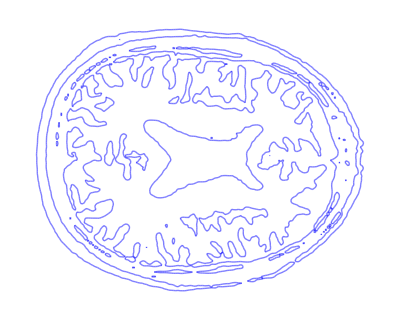

```mathematica
showCurveNoPoints[contour2D[brain,80],RGBColor[0,0,1,0.5]]
```

```mathematica
Show[showGrayImage[brain],showCurveNoPoints[contour2D[brain,80],RGBColor[0,0,1,0.5]]]
```

-Graphics-

### Contouring a 3D density volume [4 pts]

Problem 2: [2 pts] The volume "cryo.dat" is a downsampled density volume of a protein imaged with cryo-electron microscopy (you can load it in using Get command, which will return a 3D array). The protein is a folded sequence of amino acids, and visually looks like a winded-up chain. Compute an iso-surface at an approximate iso-value so that the surface has a similar look to the following:

-Graphics3D-

Problem 3: [2 pts] The volume "foot.dat" is a downsampled CT scan of a human foot (you can load it in using Get command, which will return a 3D array). Different tissues exhibit different levels of intensity in the volume. For example, the skin has a lower density than the bones. Compute iso-surfaces at two iso-values that outline respectively the skin and the bones, as shown below:

```mathematica
-Graphics3D--Graphics3D-
```

-Graphics3D- -Graphics3D-